# Notebook 04: Polygons

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Drawing polygons by specifying points

We can draw a polygon by specifying a series of points. The Graphics command will automatically close the object by drawing a line from the last point we specify to the first, and then will fill the outline with the default colour. Here is how we draw a triangle that is leaning over a bit...

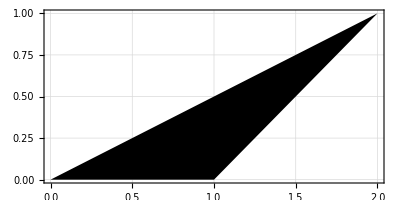

```mathematica
Graphics[Polygon[{{0,0},{2,1},{1,0}}],GridLines->Automatic,Frame->True]
```

Here is a more complicated shape.

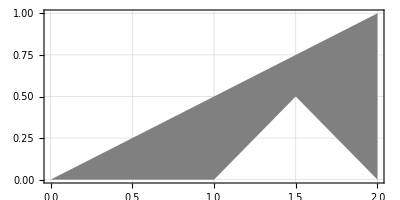

```mathematica
Graphics[{Gray,Polygon[{{0,0},{2,1},{2,0},{3/2,1/2},{1,0}}]},GridLines->Automatic,Frame->True]
```

Two of the lines in this polygon cross one another, leading to an hourglass shape.

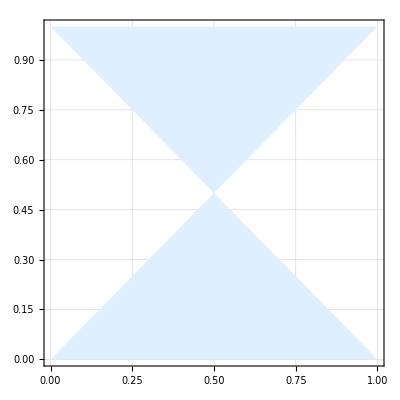

```mathematica
Graphics[{LightBlue,Polygon[{{0,0},{1,1},{0,1},{1,0}}]},GridLines->Automatic,Frame->True]
```

Make sure you understand why the point {1/2, 1/2} is not explicitly specified in the example above, then look at the next figure.

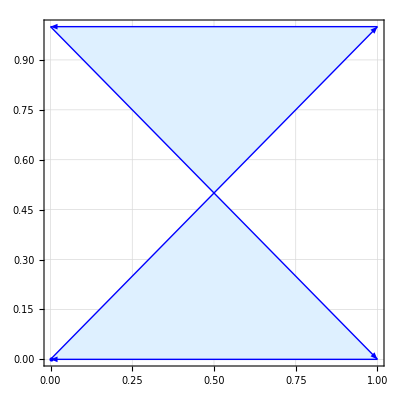

```mathematica
Graphics[{LightBlue,Polygon[{{0,0},{1,1},{0,1},{1,0}}],Blue,PointSize[Large],Point[{0,0}],Arrow[{{0,0},{1,1}}],Arrow[{{1,1},{0,1}}],Arrow[{{0,1},{1,0}}],Arrow[{{1,0},{0,0}}]},GridLines->Automatic,Frame->True]
```

Try drawing the hourglass shape with two polygons instead of one.

## Opacity and transparency

You can set the Opacity of an object to a value between 1 (opaque) and 0 (completely transparent). In the image below, a half-transparent blue disk is drawn on top of a fully opaque one.

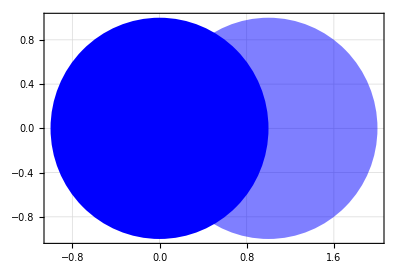

```mathematica
Graphics[{Blue,Disk[{0,0},1],Opacity[1/2],Disk[{1,0},1]},GridLines->Automatic,Frame->True]
```

If we change the colour of the second disk it is easier to see that it overlaps the first one...

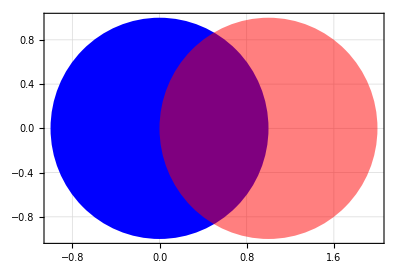

```mathematica
Graphics[{Blue,Disk[{0,0},1],Red,Opacity[1/2],Disk[{1,0},1]},GridLines->Automatic,Frame->True]
```

### Seeing through elements

Here is an example of using opacity to allow elements at a lower level to show through

```mathematica
face={Blue,Disk[{3,2},1.8],Yellow,Disk[{3,2},1.75],Blue,Disk[{2,2.5},1/4],Disk[{4,2.5},1/4],Rectangle[{2,1.15},{4,1.35}]};
```

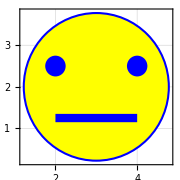

```mathematica
Graphics[face,GridLines->Automatic,Frame->True]
```

```mathematica
helmet={LightGray,Polygon[{{1,3},{2,4},{4,4},{5,3}}],Polygon[{{1,1},{5,1},{4,0},{2,0},{1,1}}],Black,Opacity[1/2],Rectangle[{1,1},{5,3}]};
```

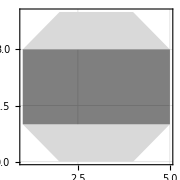

```mathematica
Graphics[helmet,GridLines->Automatic,Frame->True]
```

Now the two combined

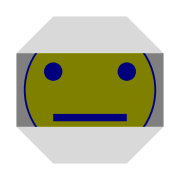

```mathematica
Graphics[Join[face,helmet]]
```

## CirclePoints

The CirclePoints command figures out where to place objects if you want to distribute them evenly around the circumference of a Circle or Disk with a radius of 1 unit.

Suppose you want to place 3 items. The blue points indicate where their centres would be.

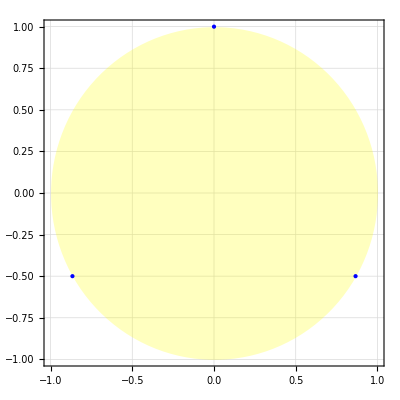

```mathematica
Graphics[{Yellow,Opacity[1/4], Disk[],Opacity[1],PointSize[Large],Blue,Point[CirclePoints[3]]},GridLines->Automatic,Frame->True]
```

If you want to place seven items

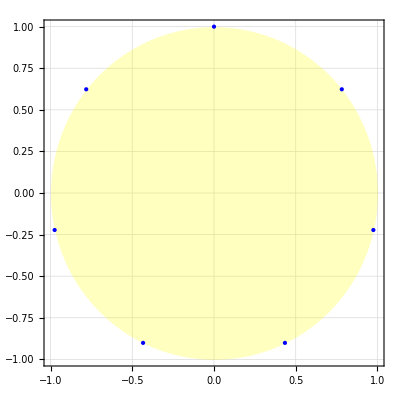

```mathematica
Graphics[{Yellow,Opacity[1/4], Disk[],Opacity[1],PointSize[Large],Blue,Point[CirclePoints[7]]},GridLines->Automatic,Frame->True]
```

## Regular Polygons

The CirclePoints command makes it easy to draw regular polygons

### Triangle

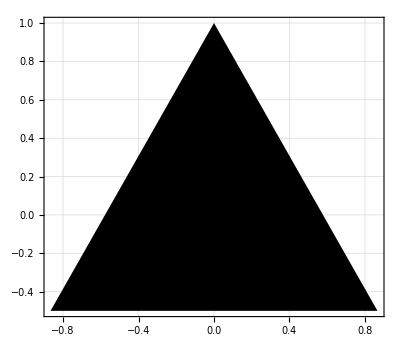

```mathematica
Graphics[Polygon[CirclePoints[3]],GridLines->Automatic,Frame->True]
```

### Pentagon

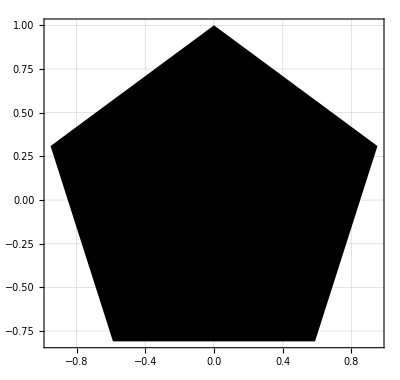

```mathematica
Graphics[Polygon[CirclePoints[5]],GridLines->Automatic,Frame->True]
```

### Hexagon

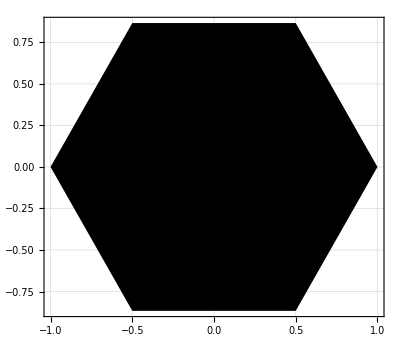

```mathematica
Graphics[Polygon[CirclePoints[6]],GridLines->Automatic,Frame->True]
```

### Septagon

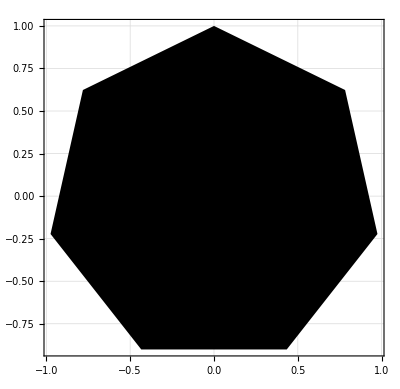

```mathematica
Graphics[Polygon[CirclePoints[7]],GridLines->Automatic,Frame->True]
```

### Lists of coordinates

Note that the CirclePoints command is actually returning a list of coordinates. Calculating these coordinates requires trigonometry (but you don’t have to know how it is done). Here are the coordinates for the seven-sided figure, the septagon.

```mathematica
CirclePoints[7]
```

{{Sin[π/7],-Cos[π/7]},{Cos[π/14],-Sin[π/14]},{Cos[(3 π)/14],Sin[(3 π)/14]},{0,1},{-Cos[(3 π)/14],Sin[(3 π)/14]},{-Cos[π/14],-Sin[π/14]},{-Sin[π/7],-Cos[π/7]}}

## Text

We can use the Text command to add text to our graphics. Note that the default size of text is quite small, and that it is drawn so that its bounding box is centred at {0, 0} by default. The bounding box is the smallest rectangle that can be drawn around a graphical element and still contain all of it.

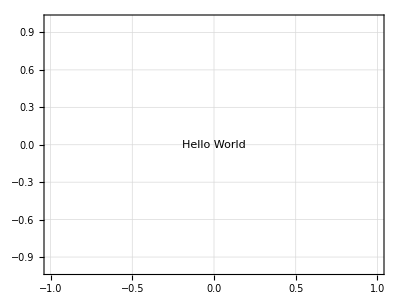

```mathematica
Graphics[Text["Hello World"],GridLines->Automatic,Frame->True]
```

We can make the text larger with the Style command (and change its colour, size, etc.)

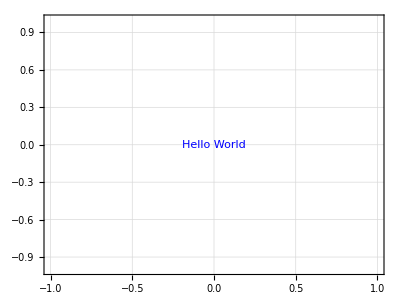

```mathematica
Graphics[Text[Style["Hello World",Medium,Blue]],GridLines->Automatic,Frame->True]
```

We can provide coordinates for the centre of the bounding box, and change font family and face too.

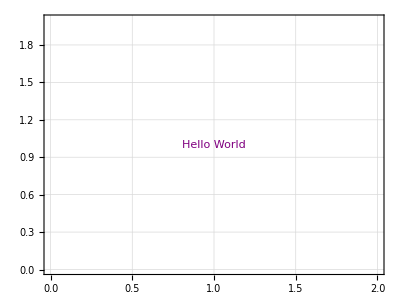

```mathematica
Graphics[Text[Style["Hello World",Large,Purple,Italic,FontFamily->"Courier"],{1,1}],GridLines->Automatic,Frame->True]
```

## In-Class Activity

### Draw a picture using the Graphics command. Use polygons and text, and make sure to change the opacity of one element in your scene (e.g., window, sunglasses, body of water, cloud, etc.)

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course